```mathematica
Clear["Global`*"]
x1 = Sqrt[1+x];
x4 = Sqrt[1 - x];
y1 = Sqrt[1+y];
y4 = Sqrt[1-y];
η = Sqrt[f + g y + y^2];
ξ = Sqrt[f + g x + x^2];
A = x1 ξ / x4 - y1 η / y4
```

```mathematica
U =( x1 x4 η + y1 y4 ξ)/(x - y);
```

```mathematica
B = -(f + g + 1) x1 y1 / (x4 y4 U);
```

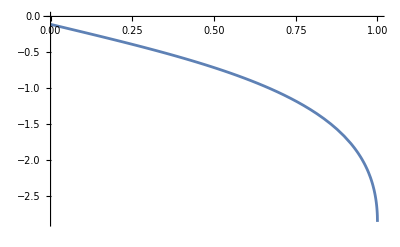

```mathematica
Plot[A + B/.f->6.57894737/.g->-1.14832536/.x->-0.1,{y,0,1}]
```

```mathematica
A + B//FullSimplify
```

((x-y) (-√(1+x) √(1+y)+√(1+x) √(1+y) (x+y-x y)+√(1-x) √(f+x (g+x)) √(1-y) √(f+y (g+y))))/(√(1-x) √(1-y) (√(f+x (g+x)) √(1-y^2)+√(1-x^2) √(f+y (g+y))))

```mathematica
Limit[A+B,y->1]
```

((-1+x) √(f+x (g+x)))/(√(1-x^2))

```mathematica
-x4 * ξ / x1
```

-(√(1-x) √(f+g x+x^2))/(√(1+x))

```mathematica
Limit[A+B,x->1]
```

-((-1+y) √(f+y (g+y)))/(√(1-y^2))

```mathematica
B
```

((-1-f-g) √(1+x) (x-y) √(1+y))/(√(1-x) √(1-y) (√(f+g x+x^2) √(1-y) √(1+y)+√(1-x) √(1+x) √(f+g y+y^2)))

```mathematica
ArcTan[-1000000.0]
```

-1.5708